# Quasi-reversible cyclic voltammetry with coupled homogeneous reaction

## Fully implicit method

This notebook shows how a cyclic voltammogram for the simple quasi-reversible reaction with a coupled chemical reaction

O+e ⇌R
R ⇌_(k_-1)^(k_(+1)) P

can be simulated using implicit finite difference methods.

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.5]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
optionA={
PlotRange->{{upperLimit+1,lowerLimit-1},{-0.55,0.4}},
PlotStyle->{Red,AbsoluteThickness[0.5]},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12,FontColor->Black, FontSlant->Italic],
Style["√πχ",FontFamily->  "Times New Roman",FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None}
};
```

```mathematica
$Line=0;
```

## Make diagonals

```mathematica
Clear[makeCoupledDiagonals];

makeCoupledDiagonals[j_Integer,d_][khf_,khb_]:=Module[{x,y,z},
x=Table[-d*IdentityMatrix[3],{j}];
z=Table[-d*IdentityMatrix[3],{j}];
y=Table[(1+2*d)*IdentityMatrix[3]+{{0,0,0},{0,khf,-khb},{0,-khf,khb}},{j}];
x⟦1,3,3⟧=0;
y⟦1,3,3⟧-=4*d/3;
z⟦1,3,3⟧+=d/3;
{x,y,z}]
```

```mathematica
Clear[𝔻,khf,khb];
makeCoupledDiagonals[5,𝔻][khf,khb]
```

{{{{-𝔻,0,0},{0,-𝔻,0},{0,0,0}},{{-𝔻,0,0},{0,-𝔻,0},{0,0,-𝔻}},{{-𝔻,0,0},{0,-𝔻,0},{0,0,-𝔻}},{{-𝔻,0,0},{0,-𝔻,0},{0,0,-𝔻}},{{-𝔻,0,0},{0,-𝔻,0},{0,0,-𝔻}}},{{{1+2 𝔻,0,0},{0,1+khf+2 𝔻,-khb},{0,-khf,1+khb+(2 𝔻)/3}},{{1+2 𝔻,0,0},{0,1+khf+2 𝔻,-khb},{0,-khf,1+khb+2 𝔻}},{{1+2 𝔻,0,0},{0,1+khf+2 𝔻,-khb},{0,-khf,1+khb+2 𝔻}},{{1+2 𝔻,0,0},{0,1+khf+2 𝔻,-khb},{0,-khf,1+khb+2 𝔻}},{{1+2 𝔻,0,0},{0,1+khf+2 𝔻,-khb},{0,-khf,1+khb+2 𝔻}}},{{{-𝔻,0,0},{0,-𝔻,0},{0,0,-(2 𝔻)/3}},{{-𝔻,0,0},{0,-𝔻,0},{0,0,-𝔻}},{{-𝔻,0,0},{0,-𝔻,0},{0,0,-𝔻}},{{-𝔻,0,0},{0,-𝔻,0},{0,0,-𝔻}},{{-𝔻,0,0},{0,-𝔻,0},{0,0,-𝔻}}}}

## Set Up Solution

```mathematica
Clear[tridiagMatSolver];

tridiagMatSolver=Compile[{{x,_Real,3},{y,_Real,3},{z,_Real,3},{b,_Real,2}},Module[{len=Length[b],sol=Table[Table[0.,{Length[b⟦1⟧]}],{Length[b]}],aux,β=Table[Table[0.,{Length[x⟦1⟧]},{Length[x⟦1⟧]}],{Length[b]}],iter=0},

aux=Inverse[y⟦1⟧];
sol⟦1⟧=aux.b⟦1⟧;
Do[β⟦iter⟧=aux.z⟦iter-1⟧;
aux=Inverse[(y⟦iter⟧-x⟦iter⟧.β⟦iter⟧)];
sol⟦iter⟧=aux.(b⟦iter⟧-x⟦iter⟧.sol⟦iter-1⟧),{iter,2,len}]; 			Do[sol⟦iter⟧-=β⟦iter+1⟧.sol⟦iter+1⟧,{iter,len-1,1,-1}];
sol]];
```

```mathematica
Clear[implicitSolveCoupled];

implicitSolveCoupled[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_},{ksStar_,khf_,khb_,α_}]:=Module[{x,y,z,y1,xstar,z1,b2,initial,range,τ,solveNext},

range=2*(upperLimit+Abs[lowerLimit]);
τ=range/(n-1);

{x,y,z}=makeCoupledDiagonals[m,d][khf,khb];
xstar=x⟦1,{1,2},{1,2}⟧;
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[{1.,0.,0.},{m}];
b2={{1,0},{1,1}};

solveNext[list_List,k_Integer]:=Module[{ξ,b,b1,tmp2},

ξ=If[k>(n+1)/2,Exp[upperLimit-range+(τ*(k-1))],Exp[upperLimit-(τ*(k-1))]];
y⟦1⟧=y1;
z⟦1⟧=z1;
b=list[[2;;-2]];
b⟦-1⟧+={d,0.,0.};
b1=Inverse[{{3+2*ksStar*ξ^-α,-2*ksStar*ξ^(1.-α)},{3,3}}];
y⟦1,{1,2},{1,2}⟧+=4*(xstar.b1.b2);
z⟦1,{1,2},{1,2}⟧-=xstar.b1.b2;
tmp2=tridiagMatSolver[x,y,z,b];
Join[{Join[(4*b1.b2.tmp2⟦1,{1,2}⟧-b1.b2.tmp2⟦2,{1,2}⟧),{(4*tmp2⟦1,3⟧-tmp2⟦2,3⟧)/3}]},tmp2,{{1.,0.,0.}}]
];

FoldList[solveNext,initial,Range[2,n]]
]
```

## Set Parameter Values

### Set Constants & variables

```mathematica
Clear[α,𝒟,F,R,T,f];

(*set the value of constants*)

α=0.5(*transfer coefficient, generally taken as being 0.5*);

𝒟=1.*^-5(*diffusion coefficient - assumed to be the same for all species*);

F=96485.(*Faradays constant*);

R=8.3144(*gas constant*);

T=298.(*temperature in Kelvin*);

f=F/(R*T);
```

### Set Electrochemical variables

```mathematica
Clear[upperLimit,lowerLimit,𝕥,ksDim];

upperLimit=10.(*initial potential versus the formal potential*);

lowerLimit=-10.(*switching potential versus the formal potential*);

𝕥 =2*(upperLimit+Abs[lowerLimit]);(*the region or range of the sweep*)

ksDim=1.*^0(*dimensionless rate constant*);
```

### Set Simulation Variables

```mathematica
Clear[n,τ,khf,khb,𝔻,m,ksStar]

n=Round[𝕥/(0.005*f)];(*5 mV steps*)

τ=𝕥/(n-1);(*calculation of the incremental time/potential step*)

khf=τ*5.;(*dimensionless homogeneous forward rate constant*)

khb=τ*1.;(*dimensionless homogeneous backward rate constant*)

𝔻=5.*Max[khb,khf,.4];(*model diffusion coefficient*)

m=Ceiling[6*√(𝔻*(n-1))];(*number of spacial grid points*)

ksStar=ksDim*Sqrt[𝕥/(𝔻*(n-1))];(*dimensionless rate constant*)
```

```mathematica
{n,τ,khf,khb,𝔻,m,ksStar}
```

{205,0.196078,0.980392,0.196078,4.90196,190,0.2}

## Solve it

```mathematica
c=implicitSolveCoupled[m,n,𝔻,{lowerLimit,upperLimit},{ksStar,khf,khb,α}];
```

## Plot CV

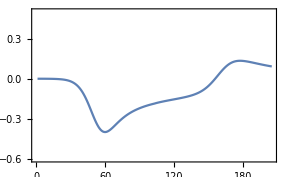

```mathematica
cv1=Map[(((3*#⟦1⟧-4*#⟦2⟧+#⟦3⟧)/2)*√((𝔻*(n-1))/𝕥))&,c⟦All,All,1⟧];

plot1=ListPlot[cv1,PlotRange-> {Automatic,{-.6,.5}}]
```

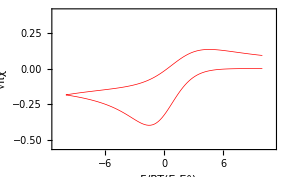

```mathematica
cv2=Table[{If[j>(n+1)/2,upperLimit-𝕥+τ*(j-1),upperLimit-(𝕥*(j-1)/(n-1))],cv1⟦j⟧},{j,1,Length[cv1]}];

plot2=ListPlot[cv2,optionA]
```